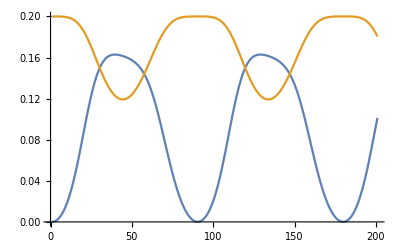

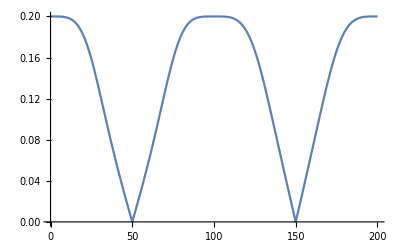

```mathematica
ClearAll["Global`*"];
qubitmatrixToCartesian[Mq_]:=(
q1=Re[(Mq[[1,2]]+Mq[[2,1]])/2];
q2=Re[(Mq[[2,1]]-Mq[[1,2]])/(2*I)];
q3=Re[Mq[[1,1]]];
Return[{q1,q2,q3}];
);

rnSU2euler[vec_,rx_,ry_,rz_]:=(
sphericalVec = ToSphericalCoordinates[vec];
θ=sphericalVec[[2]];
ϕ=sphericalVec[[3]];
sx=PauliMatrix[1];
sy=PauliMatrix[2];
sz=PauliMatrix[3];
Mq=Sin[θ]*Cos[ϕ]*sx+Sin[θ]*Sin[ϕ]*sy+Cos[θ]*sz;
Un={{Exp[-I*(rx+rz)/2]*Cos[ry/2],-Exp[-I*(rx-rz)/2]*Sin[ry/2]},{Exp[I*(rx-rz)/2]*Sin[ry/2],Exp[I*(rx+rz)/2]*Cos[ry/2]}};
Return [Un.Mq.ConjugateTranspose[Un]];
);

rotateVector[vec_,rx_,ry_,rz_]:=(
MqRotated=rnSU2euler[vec,rx,ry,rz];
Return[qubitmatrixToCartesian[MqRotated]];
);
subtractAngles[a1_,a2_]:=(
d=Abs[a1-a2];
Return[Min[d,2*Pi-d]];
);
errorPropagation[n_,vec_,vecError_,rx_,ry_,rz_]:=(
(*v=NestList[N[rotateVector[#,rx,ry,rz]]&,vec,n];
vErr=NestList[N[rotateVector[#,rx,ry,rz]]&,vecError,n];*)
v=NestList[rotateVector[#,rx,ry,rz]&,N@vec,n];
vErr=NestList[rotateVector[#,rx,ry,rz]&,N@vecError,n];
spherical=Map[ToSphericalCoordinates,v];
sphericalErr=Map[ToSphericalCoordinates,vErr];
{MapThread[subtractAngles,{sphericalErr[[All,3]],spherical[[All,3]]}],MapThread[subtractAngles,{sphericalErr[[All,2]],spherical[[All,2]]}]}
);

ListLinePlot[errorPropagation[200,{1,0,0},N[rotateVector[{1,0,0},0,0.2,0]],Pi/100,Pi/100,Pi/100]]
Plot[subtractAngles[
ToSphericalCoordinates[N[rotateVector[N[rotateVector[{1,0,0},0,0.2,0]],n*Pi/100,n*Pi/100,n*Pi/100]]][[2]],
ToSphericalCoordinates[N[rotateVector[{1,0,0},n*Pi/100,n*Pi/100,n*Pi/100]]][[2]]],
{n,0,200}]
```

```mathematica
Fourier[{0,2,0.1999999,0.1999984,0.19999183,0.199974,0.19993605,0.19986638,0.19975062,0.19957154,0.19930918,0.198941,0.19844217,0.19778616,0.19694543,0.19589245,0.19460094,0.19304735,0.19121243,0.18908285,0.18665275,0.18392492,0.18091154,0.17763437,0.1741243,0.17042018,0.16656727,0.16261523,0.15861597,0.15462159,0.1506825,0.14684594,0.14315484,0.13964714,0.13635548,0.13330722,0.13052469,0.12802557,0.12582347,0.1239284,0.12234735,0.12108479,0.12014311,0.11952299,0.11922366,0.11924317,0.11957845,0.12022542,0.12117896,0.12243277,0.12397932,0.12580956,0.12791272,0.13027604,0.13288445,0.13572028,0.13876305,0.1419892,0.14537205,0.14888177,0.15248557,0.15614806,0.15983187,0.16349834,0.16710858,0.17062449,0.17401001,0.1772323,0.1802628,0.18307817,0.18566091,0.18799978,0.19008972,0.19193168,0.19353197,0.19490159,0.1960553,0.19701072,0.19778738,0.19840589,0.19888714,0.1992517,0.19951924,0.19970817,0.19983532,0.1999157,0.19996238,0.19998635,0.19999652,0.19999957,0.2}]
```

{1.78209+0. ⅈ,0.364565+0.00531791 ⅈ,0.118224+0.0327741 ⅈ,0.158418+0.037265 ⅈ,0.162843+0.0508842 ⅈ,0.156866+0.0640144 ⅈ,0.15166+0.0759984 ⅈ,0.146105+0.0876782 ⅈ,0.139675+0.0990048 ⅈ,0.132454+0.109855 ⅈ,0.124508+0.120176 ⅈ,0.11587+0.129926 ⅈ,0.10658+0.139057 ⅈ,0.0966819+0.147525 ⅈ,0.0862235+0.15529 ⅈ,0.0752544+0.162315 ⅈ,0.0638268+0.168567 ⅈ,0.0519951+0.174015 ⅈ,0.0398158+0.178634 ⅈ,0.0273467+0.182402 ⅈ,0.0146475+0.1853 ⅈ,0.00177859+0.187316 ⅈ,-0.0111987+0.188438 ⅈ,-0.0242226+0.188663 ⅈ,-0.0372309+0.187989 ⅈ,-0.0501617+0.186419 ⅈ,-0.0629534+0.18396 ⅈ,-0.075545+0.180625 ⅈ,-0.0878765+0.176429 ⅈ,-0.0998892+0.171393 ⅈ,-0.111526+0.165539 ⅈ,-0.122731+0.158897 ⅈ,-0.133451+0.151498 ⅈ,-0.143635+0.143376 ⅈ,-0.153234+0.134571 ⅈ,-0.162203+0.125125 ⅈ,-0.170499+0.115083 ⅈ,-0.178083+0.104492 ⅈ,-0.184917+0.0934038 ⅈ,-0.190971+0.0818701 ⅈ,-0.196214+0.0699462 ⅈ,-0.200622+0.0576889 ⅈ,-0.204174+0.0451568 ⅈ,-0.206853+0.0324094 ⅈ,-0.208646+0.0195076 ⅈ,-0.209545+0.00651289 ⅈ,-0.209545-0.00651289 ⅈ,-0.208646-0.0195076 ⅈ,-0.206853-0.0324094 ⅈ,-0.204174-0.0451568 ⅈ,-0.200622-0.0576889 ⅈ,-0.196214-0.0699462 ⅈ,-0.190971-0.0818701 ⅈ,-0.184917-0.0934038 ⅈ,-0.178083-0.104492 ⅈ,-0.170499-0.115083 ⅈ,-0.162203-0.125125 ⅈ,-0.153234-0.134571 ⅈ,-0.143635-0.143376 ⅈ,-0.133451-0.151498 ⅈ,-0.122731-0.158897 ⅈ,-0.111526-0.165539 ⅈ,-0.0998892-0.171393 ⅈ,-0.0878765-0.176429 ⅈ,-0.075545-0.180625 ⅈ,-0.0629534-0.18396 ⅈ,-0.0501617-0.186419 ⅈ,-0.0372309-0.187989 ⅈ,-0.0242226-0.188663 ⅈ,-0.0111987-0.188438 ⅈ,0.00177859-0.187316 ⅈ,0.0146475-0.1853 ⅈ,0.0273467-0.182402 ⅈ,0.0398158-0.178634 ⅈ,0.0519951-0.174015 ⅈ,0.0638268-0.168567 ⅈ,0.0752544-0.162315 ⅈ,0.0862235-0.15529 ⅈ,0.0966819-0.147525 ⅈ,0.10658-0.139057 ⅈ,0.11587-0.129926 ⅈ,0.124508-0.120176 ⅈ,0.132454-0.109855 ⅈ,0.139675-0.0990048 ⅈ,0.146105-0.0876782 ⅈ,0.15166-0.0759984 ⅈ,0.156866-0.0640144 ⅈ,0.162843-0.0508842 ⅈ,0.158418-0.037265 ⅈ,0.118224-0.0327741 ⅈ,0.364565-0.00531791 ⅈ}

```mathematica
Fourier[{0,0.000201481185,0.000812500741,0.00184508687,0.00331397024,0.00523619047,0.00763047464,0.0105163489,0.013912944,0.0178374635,0.022303301,0.0273178244,0.0328798936,0.0389772395,0.0455839108,0.0526580653,0.0601404489,0.0679539219,0.076004356,0.0841831101,0.0923710988,0.100444228,0.108279727,0.115762712,0.122792246,0.129286219,0.135184541,0.140450442,0.145069925,0.149049663,0.152413799,0.155200116,0.157456051,0.159234911,0.160592529,0.161584505,0.162264057,0.162680454,0.162877959,0.16289519,0.162764791,0.162513338,0.1621614,0.161723684,0.161209239,0.160621668,0.159959352,0.15921566,0.158379173,0.157433912,0.15635961,0.155132055,0.153723529,0.152103392,0.150238838,0.148095874,0.145640528,0.142840305,0.139665859,0.136092848,0.132103861,0.127690297,0.122854042,0.117608748,0.111980548,0.106008062,0.0997416169,0.093241664,0.0865765085,0.0798195185,0.0730460641,0.0663304597,0.0597431699,0.0533484938,0.0472028675,0.0413538424,0.0358397236,0.0306897876,0.0259249646,0.0215588528,0.017598936,0.0140478896,0.0109048865,0.00816683509,0.00582950776,0.00388853601,0.00234026229,0.00118244856,0.000414846086,0.0000396315171}]
```

{0.852566+0. ⅈ,-0.403738+0.0441027 ⅈ,-0.0490667-0.0110975 ⅈ,0.0235286-0.0076055 ⅈ,0.00355516+0.00123791 ⅈ,-0.00113005+0.000743587 ⅈ,-0.000110076-0.000108449 ⅈ,0.00016639-0.0000726968 ⅈ,0.0000897589-1.88307×10^-6 ⅈ,0.000053188-2.97869×10^-6 ⅈ,0.0000448754-7.87371×10^-6 ⅈ,0.0000382963-7.35335×10^-6 ⅈ,0.0000320081-6.45333×10^-6 ⅈ,0.0000270615-5.98215×10^-6 ⅈ,0.0000232135-5.59074×10^-6 ⅈ,0.0000201124-5.20794×10^-6 ⅈ,0.0000175672-4.85351×10^-6 ⅈ,0.0000154571-4.52871×10^-6 ⅈ,0.0000136915-4.23072×10^-6 ⅈ,0.0000121993-3.9546×10^-6 ⅈ,0.000010929-3.69766×10^-6 ⅈ,9.83864×10^-6-3.45906×10^-6 ⅈ,8.89831×10^-6-3.23544×10^-6 ⅈ,8.08149×10^-6-3.02564×10^-6 ⅈ,7.36974×10^-6-2.82758×10^-6 ⅈ,6.74624×10^-6-2.64096×10^-6 ⅈ,6.19774×10^-6-2.46333×10^-6 ⅈ,5.71536×10^-6-2.29436×10^-6 ⅈ,5.28837×10^-6-2.13327×10^-6 ⅈ,4.91072×10^-6-1.97871×10^-6 ⅈ,4.57614×10^-6-1.82999×10^-6 ⅈ,4.27976×10^-6-1.68759×10^-6 ⅈ,4.01715×10^-6-1.54892×10^-6 ⅈ,3.7846×10^-6-1.41493×10^-6 ⅈ,3.57956×10^-6-1.2852×10^-6 ⅈ,3.3995×10^-6-1.15837×10^-6 ⅈ,3.24167×10^-6-1.03455×10^-6 ⅈ,3.10471×10^-6-9.13397×10^-7 ⅈ,2.98717×10^-6-7.94653×10^-7 ⅈ,2.88784×10^-6-6.77554×10^-7 ⅈ,2.8047×10^-6-5.62318×10^-7 ⅈ,2.73869×10^-6-4.4812×10^-7 ⅈ,2.68739×10^-6-3.35439×10^-7 ⅈ,2.65137×10^-6-2.2303×10^-7 ⅈ,2.62981×10^-6-1.11403×10^-7 ⅈ,2.62277×10^-6+4.47497×10^-19 ⅈ,2.62981×10^-6+1.11403×10^-7 ⅈ,2.65137×10^-6+2.2303×10^-7 ⅈ,2.68739×10^-6+3.35439×10^-7 ⅈ,2.73869×10^-6+4.4812×10^-7 ⅈ,2.8047×10^-6+5.62318×10^-7 ⅈ,2.88784×10^-6+6.77554×10^-7 ⅈ,2.98717×10^-6+7.94653×10^-7 ⅈ,3.10471×10^-6+9.13397×10^-7 ⅈ,3.24167×10^-6+1.03455×10^-6 ⅈ,3.3995×10^-6+1.15837×10^-6 ⅈ,3.57956×10^-6+1.2852×10^-6 ⅈ,3.7846×10^-6+1.41493×10^-6 ⅈ,4.01715×10^-6+1.54892×10^-6 ⅈ,4.27976×10^-6+1.68759×10^-6 ⅈ,4.57614×10^-6+1.82999×10^-6 ⅈ,4.91072×10^-6+1.97871×10^-6 ⅈ,5.28837×10^-6+2.13327×10^-6 ⅈ,5.71536×10^-6+2.29436×10^-6 ⅈ,6.19774×10^-6+2.46333×10^-6 ⅈ,6.74624×10^-6+2.64096×10^-6 ⅈ,7.36974×10^-6+2.82758×10^-6 ⅈ,8.08149×10^-6+3.02564×10^-6 ⅈ,8.89831×10^-6+3.23544×10^-6 ⅈ,9.83864×10^-6+3.45906×10^-6 ⅈ,0.000010929+3.69766×10^-6 ⅈ,0.0000121993+3.9546×10^-6 ⅈ,0.0000136915+4.23072×10^-6 ⅈ,0.0000154571+4.52871×10^-6 ⅈ,0.0000175672+4.85351×10^-6 ⅈ,0.0000201124+5.20794×10^-6 ⅈ,0.0000232135+5.59074×10^-6 ⅈ,0.0000270615+5.98215×10^-6 ⅈ,0.0000320081+6.45333×10^-6 ⅈ,0.0000382963+7.35335×10^-6 ⅈ,0.0000448754+7.87371×10^-6 ⅈ,0.000053188+2.97869×10^-6 ⅈ,0.0000897589+1.88307×10^-6 ⅈ,0.00016639+0.0000726968 ⅈ,-0.000110076+0.000108449 ⅈ,-0.00113005-0.000743587 ⅈ,0.00355516-0.00123791 ⅈ,0.0235286+0.0076055 ⅈ,-0.0490667+0.0110975 ⅈ,-0.403738-0.0441027 ⅈ}